# Basic plotting: getting used to notebook programming

```mathematica
(sinSeries=Table[ N[Sin[n x ]],{x, 0, 2 Pi, 2 Pi/15}, {n, 0, 15}]) //TableForm
```

0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.406737 | 0.743145 | 0.951057 | 0.994522 | 0.866025 | 0.587785 | 0.207912 | -0.207912 | -0.587785 | -0.866025 | -0.994522 | -0.951057 | -0.743145 | -0.406737 | 0.
0. | 0.743145 | 0.994522 | 0.587785 | -0.207912 | -0.866025 | -0.951057 | -0.406737 | 0.406737 | 0.951057 | 0.866025 | 0.207912 | -0.587785 | -0.994522 | -0.743145 | 0.
0. | 0.951057 | 0.587785 | -0.587785 | -0.951057 | 0. | 0.951057 | 0.587785 | -0.587785 | -0.951057 | 0. | 0.951057 | 0.587785 | -0.587785 | -0.951057 | 0.
0. | 0.994522 | -0.207912 | -0.951057 | 0.406737 | 0.866025 | -0.587785 | -0.743145 | 0.743145 | 0.587785 | -0.866025 | -0.406737 | 0.951057 | 0.207912 | -0.994522 | 0.
0. | 0.866025 | -0.866025 | 0. | 0.866025 | -0.866025 | 0. | 0.866025 | -0.866025 | 0. | 0.866025 | -0.866025 | 0. | 0.866025 | -0.866025 | 0.
0. | 0.587785 | -0.951057 | 0.951057 | -0.587785 | 0. | 0.587785 | -0.951057 | 0.951057 | -0.587785 | 0. | 0.587785 | -0.951057 | 0.951057 | -0.587785 | 0.
0. | 0.207912 | -0.406737 | 0.587785 | -0.743145 | 0.866025 | -0.951057 | 0.994522 | -0.994522 | 0.951057 | -0.866025 | 0.743145 | -0.587785 | 0.406737 | -0.207912 | 0.
0. | -0.207912 | 0.406737 | -0.587785 | 0.743145 | -0.866025 | 0.951057 | -0.994522 | 0.994522 | -0.951057 | 0.866025 | -0.743145 | 0.587785 | -0.406737 | 0.207912 | 0.
0. | -0.587785 | 0.951057 | -0.951057 | 0.587785 | 0. | -0.587785 | 0.951057 | -0.951057 | 0.587785 | 0. | -0.587785 | 0.951057 | -0.951057 | 0.587785 | 0.
0. | -0.866025 | 0.866025 | 0. | -0.866025 | 0.866025 | 0. | -0.866025 | 0.866025 | 0. | -0.866025 | 0.866025 | 0. | -0.866025 | 0.866025 | 0.
0. | -0.994522 | 0.207912 | 0.951057 | -0.406737 | -0.866025 | 0.587785 | 0.743145 | -0.743145 | -0.587785 | 0.866025 | 0.406737 | -0.951057 | -0.207912 | 0.994522 | 0.
0. | -0.951057 | -0.587785 | 0.587785 | 0.951057 | 0. | -0.951057 | -0.587785 | 0.587785 | 0.951057 | 0. | -0.951057 | -0.587785 | 0.587785 | 0.951057 | 0.
0. | -0.743145 | -0.994522 | -0.587785 | 0.207912 | 0.866025 | 0.951057 | 0.406737 | -0.406737 | -0.951057 | -0.866025 | -0.207912 | 0.587785 | 0.994522 | 0.743145 | 0.
0. | -0.406737 | -0.743145 | -0.951057 | -0.994522 | -0.866025 | -0.587785 | -0.207912 | 0.207912 | 0.587785 | 0.866025 | 0.994522 | 0.951057 | 0.743145 | 0.406737 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

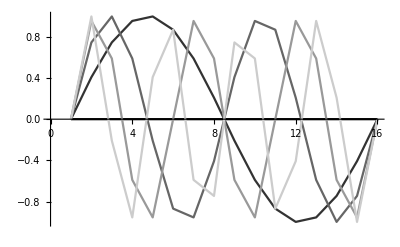

```mathematica
ListLinePlot[sinSeries[[1 ;;5]], PlotStyle-> Table[GrayLevel[n/5],{n,0, 15}]]
```

```mathematica
(cosSeries=Table[ N[Cos[n x ]],{x, 0, 2 Pi, 2 Pi/15}, {n, 0, 15}]) //TableForm
```

1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 0.913545 | 0.669131 | 0.309017 | -0.104528 | -0.5 | -0.809017 | -0.978148 | -0.978148 | -0.809017 | -0.5 | -0.104528 | 0.309017 | 0.669131 | 0.913545 | 1.
1. | 0.669131 | -0.104528 | -0.809017 | -0.978148 | -0.5 | 0.309017 | 0.913545 | 0.913545 | 0.309017 | -0.5 | -0.978148 | -0.809017 | -0.104528 | 0.669131 | 1.
1. | 0.309017 | -0.809017 | -0.809017 | 0.309017 | 1. | 0.309017 | -0.809017 | -0.809017 | 0.309017 | 1. | 0.309017 | -0.809017 | -0.809017 | 0.309017 | 1.
1. | -0.104528 | -0.978148 | 0.309017 | 0.913545 | -0.5 | -0.809017 | 0.669131 | 0.669131 | -0.809017 | -0.5 | 0.913545 | 0.309017 | -0.978148 | -0.104528 | 1.
1. | -0.5 | -0.5 | 1. | -0.5 | -0.5 | 1. | -0.5 | -0.5 | 1. | -0.5 | -0.5 | 1. | -0.5 | -0.5 | 1.
1. | -0.809017 | 0.309017 | 0.309017 | -0.809017 | 1. | -0.809017 | 0.309017 | 0.309017 | -0.809017 | 1. | -0.809017 | 0.309017 | 0.309017 | -0.809017 | 1.
1. | -0.978148 | 0.913545 | -0.809017 | 0.669131 | -0.5 | 0.309017 | -0.104528 | -0.104528 | 0.309017 | -0.5 | 0.669131 | -0.809017 | 0.913545 | -0.978148 | 1.
1. | -0.978148 | 0.913545 | -0.809017 | 0.669131 | -0.5 | 0.309017 | -0.104528 | -0.104528 | 0.309017 | -0.5 | 0.669131 | -0.809017 | 0.913545 | -0.978148 | 1.
1. | -0.809017 | 0.309017 | 0.309017 | -0.809017 | 1. | -0.809017 | 0.309017 | 0.309017 | -0.809017 | 1. | -0.809017 | 0.309017 | 0.309017 | -0.809017 | 1.
1. | -0.5 | -0.5 | 1. | -0.5 | -0.5 | 1. | -0.5 | -0.5 | 1. | -0.5 | -0.5 | 1. | -0.5 | -0.5 | 1.
1. | -0.104528 | -0.978148 | 0.309017 | 0.913545 | -0.5 | -0.809017 | 0.669131 | 0.669131 | -0.809017 | -0.5 | 0.913545 | 0.309017 | -0.978148 | -0.104528 | 1.
1. | 0.309017 | -0.809017 | -0.809017 | 0.309017 | 1. | 0.309017 | -0.809017 | -0.809017 | 0.309017 | 1. | 0.309017 | -0.809017 | -0.809017 | 0.309017 | 1.
1. | 0.669131 | -0.104528 | -0.809017 | -0.978148 | -0.5 | 0.309017 | 0.913545 | 0.913545 | 0.309017 | -0.5 | -0.978148 | -0.809017 | -0.104528 | 0.669131 | 1.
1. | 0.913545 | 0.669131 | 0.309017 | -0.104528 | -0.5 | -0.809017 | -0.978148 | -0.978148 | -0.809017 | -0.5 | -0.104528 | 0.309017 | 0.669131 | 0.913545 | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.

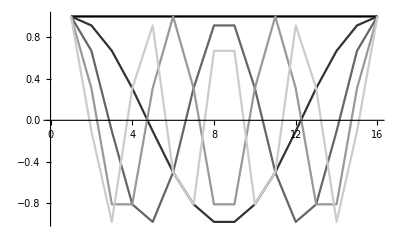

```mathematica
ListLinePlot[cosSeries[[1 ;;5]], PlotStyle-> Table[GrayLevel[n/5],{n,0, 15}]]
```